```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
(* To find the neighbours of a given site, given the number of site elements in one dimension and the number of dimensions. *)

(*In each dimension, there are two bounding surfaces. Here we determine the elements of the two surfaces for all the dimensions. The boundaries are in the format 
{{x axis boundary points}, {y axis boundary points} ... } *)
getBoundaries[nSites_, nDim_]:=Module[{ForwardBoundary, BackwardBoundary, d, n, n1},
ForwardBoundary = {};
For[d=1, d<=nDim, d=d+1,
AppendTo[ForwardBoundary, {}];
For[n=1, n<= nSites^(nDim-d), n=n+1,
For[n1 = 0, n1<nSites^(d-1), n1=n1+1,
AppendTo[ForwardBoundary[[d]], n*nSites^d - n1-1]
]
]
];
BackwardBoundary = {};
For[d=1, d<= nDim, d=d+1,
AppendTo[BackwardBoundary, {}];
Do[AppendTo[BackwardBoundary[[d]] , elem -(nSites^(d-1))(nSites-1)],
{elem, ForwardBoundary[[d]]}
]
];
{ForwardBoundary, BackwardBoundary}
];

(* Each site element will have 2*nDim neighbours, i.e. 2 in each dimension. Here we determine the 2 neighbours of each element in each of the dimensions *)
getNeighbours[nSites_, nDim_]:= Module[{boundaries, ForwardBoundary, BackwardBoundary, neighbour,nTot, n,d,nNeigh},
boundaries = getBoundaries[nSites, nDim];
ForwardBoundary = boundaries[[1]];
BackwardBoundary = boundaries[[2]];
nTot = nSites^nDim;
neighbour = <||>;
For[n=0, n<nTot, n=n+1,
nNeigh = {};
For[d=0, d<nDim, d=d+1,
(* Forward *)
If[Not[MemberQ[ForwardBoundary[[d+1]],n]],
 AppendTo[nNeigh, n+nSites^d], AppendTo[nNeigh, n-(nSites^(d))(nSites-1)]];
(* Backward *)
If[Not[MemberQ[BackwardBoundary[[d+1]],n]],
AppendTo[nNeigh, n-nSites^d],
AppendTo[nNeigh, n+(nSites^(d))(nSites-1)]]
]
AppendTo[neighbour, n-> nNeigh];
];
neighbour];

treeEqualQ[Tree1_, Tree2_]:= (Tree1[[1]] === Tree2[[1]] && Tree1[[3]] === Tree2[[3]]);

getTrees[nSites_, nDim_]:= Module[{neighbour, Trees, tree, change, count, generatedTrees, newTrees, visited, completed, checked, neighbours, unvisitedNeighbours, possibleCombinations,newTree,},

neighbour = getNeighbours[nSites, nDim];

Trees={{{},{0},{},False}}; (*links in the tree ,visited sites,checked sites, complete or incomplete*)
change=True;
SetSharedVariable[change];
While[change,
change=False;(* while there is atleast one incomplete tree *)
generatedTrees=WaitAll[
ParallelTable[(*For each tree*)
newTrees = {};
visited=tree[[2]];
checked=tree[[3]];
completed = tree[[4]];
If[completed,AppendTo[newTrees,tree],
change=True;
Do[(*For each visited site*)
If[Not[MemberQ[checked, visitedSite]],(*If site is not already checked *)
neighbours=neighbour[visitedSite];
unvisitedNeighbours=Complement[neighbours,visited];
If[unvisitedNeighbours=={}, ,possibleCombinations=Subsets[unvisitedNeighbours,{1,Length[unvisitedNeighbours]}];

Do[(*For each possible combination of links that can be added*)
newTree=tree;
Do[(*Add the links to the tree,and the sites to visited*)AppendTo[newTree[[1]],{visitedSite,site}];
newTree[[1]] = Sort[newTree[[1]]];
AppendTo[newTree[[2]],site];
AppendTo[newTree[[3]],visitedSite];
newTree[[3]] =Sort[newTree[[3]]];
,{site,combination}];
(*Check if the newTree created has visited all elements*)If[Sort[newTree[[2]]]==Range[0,nSites^nDim-1],newTree[[4]]=True, ,];
(* Append the new tree to the net of newtrees *)AppendTo[newTrees,newTree]; 
,{combination,possibleCombinations}
]
]]
,{visitedSite,visited}
]
]; newTrees
,{tree,Trees}
]];
Trees = DeleteDuplicates[Flatten[generatedTrees,1], treeEqualQ]; (* delete duplicates and replace the current set of trees by the new set *)
];
Trees];
```

```mathematica
(* Generating all possible trees for a 3x3 lattice *)

nSites = 3;
nDim = 2;
neighbour = getNeighbours[nSites, nDim];
Trees = getTrees[nSites, nDim]
```

```mathematica
DumpSave[StringJoin[{"Trees_",ToString[nSites] ,"_" ,ToString[nDim],".mx"}], Trees]
```

```mathematica
DumpSave[StringJoin[{"neighbours_",ToString[nSites] ,"_" ,ToString[nDim],".mx"}],  neighbour]
```

{<|0→{1,2,3,6},1→{2,0,4,7},2→{0,1,5,8},3→{4,5,6,0},4→{5,3,7,1},5→{3,4,8,2},6→{7,8,0,3},7→{8,6,1,4},8→{6,7,2,5}|>}

```mathematica
Get[StringJoin[{"Trees_",ToString[nSites] ,"_" ,ToString[nDim],".mx"}]] (*Get the object "Trees"*)
```

```mathematica
getVertexCoords[nSites_, nDim_] := Module[ (*Only for 2D lattices*)
{nTot, n, x, y},
vertexPos = {};
nTot = nSites^nDim;
x = 0;
y  = 0;
For[n=0, n<nTot, n=n+1, 
AppendTo[vertexPos, n->{x,y}];
If[Mod[n, nSites] == nSites-1, x = 0; y= y+1, x = x + 1];
];
vertexPos
]
showTree[nSites_, nDim_, tree_] := Module[
{links,neighbour,n, nTot, treeLinks},
links= {};
nTot = nSites^nDim;
neighbour = getNeighbours[nSites, nDim];
For[n=0, n<nTot, n=n+1,
Do[
 AppendTo[links, UndirectedEdge[Sort[{n, i}][[1]], Sort[{n, i}][[2]]]], {i, neighbour[n]}
]
];
treeLinks = Table[UndirectedEdge[link[[1]], link[[2]]], {link, tree}];
HighlightGraph[ Graph[DeleteDuplicates[links], VertexLabels->"Name", VertexCoordinates->getVertexCoords[nSites, nDim], EdgeShapeFunction->"CurvedEdge", EdgeStyle->{Gray}], Style[treeLinks, {Black, Thick}], ImageSize->Small]
]
```

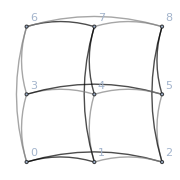
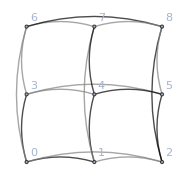
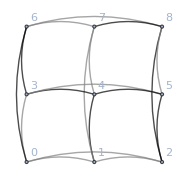
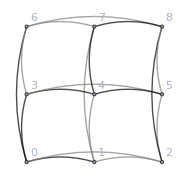
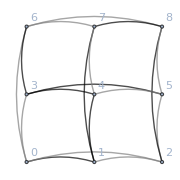
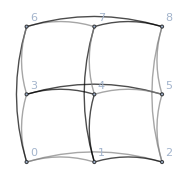
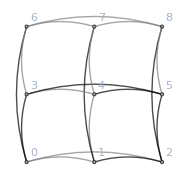
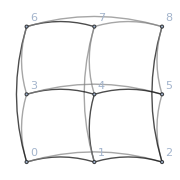
{{Index: 4974→-Graphics-},{Index: 5664→-Graphics-},{Index: 3572→-Graphics-},{Index: 10960→-Graphics-},{Index: 981→-Graphics-},{Index: 3987→-Graphics-},{Index: 9421→-Graphics-},{Index: 6761→-Graphics-}}

```mathematica
(* Showing 8 random trees from the generated trees. The thin gray lines are the links of the lattice, and the thick black lines are the links set to I via spanning tree*)
Table[index = RandomChoice[Range@Length@Trees];{StringJoin["Index: ", ToString@index]-> showTree[nSites, nDim, Trees[[ index,1]]]}, {i, Range[1,8]}]
```